## Load data, restrict to packets leaving the supernova

Restructure data such that the shape is 250 10^5 x 2  so each of the simulations is a list of 10^5 pairs (ν_i, L_i)

```mathematica
SetDirectory[NotebookDirectory[]];
h5data=Transpose[Import["real_tardis_250.h5", {"Datasets", {"/nus", "/energies"}}],{3,1,2}];
```

## Extract only packets for a single run.

```mathematica
run=10;
data=Cases[h5data[[run]],{ν_,L_} /;L>0];
sortedData=SortBy[data,First];
Dimensions[data]
(* transpose gives list with two sublist, the ν and L, WeightedData expects two separate list, so use Apply=@@ *)wd=WeightedData@@Transpose[data];
MinMax[wd["InputData"]]
binWidth=(%[[2]]-%[[1]])/1000
Histogram[wd, 2000]
```

{74784,2}

{1.47944×10^13,4.28255×10^15}

4.26775×10^12

-Graphics-

## Look at distribution of luminosity for packets as a function of frequency: For small and medium frequencies, the spectrum equals the spectrum averaged of all frequencies. But for large frequencies, it is less peaked.

```mathematica
binSpec = {ν_,L_}/;(ν≥1.199 10^15&&ν≤ 1.2 10^15&&L>0);
binspec={ν_,L_}/;(ν≥ν0&&ν≤ ν1&&L>0);
binLum=Cases[data,binSpec-> L];
Dimensions[binLum]
allBinsLumDist=SmoothKernelDistribution[Transpose[data][[2]],"Oversmooth","Triweight"];
```

{59}

```mathematica
binspec/.{ν0->1,ν1->2}
```

{ν_,L_}/;ν≥1&&ν≤2&&L>0

```mathematica
ComparisonPlot[x_,width_]:=Module[{n,pdfs},
n=Length[x];
pdfs={Map[(SmoothKernelDistribution[Cases[data,{ν_,L_}/;(ν≥#&&ν≤ #+width&&L>0)-> L],"Oversmooth","Triweight"]&),x],
allBinsLumDist}//Flatten;
Plot[Evaluate[Map[PDF[#,l]&,pdfs]],{l,1.2 10^38,1.50 10^38}]
]
ComparisonPlot[{0.3 10^15,1.5 10^15,2.1 10^15},15 binWidth]
```

-Graphics-

## Compare the sum of luminosities in a bin across simulation runs

```mathematica
(*  very slow but it works *)
lums=(Cases[#,binSpec-> L]&)/@h5data[[1;;25]];
lumSums=Total/@lums
```

{5.99775×10^39,6.88757×10^39,7.42981×10^39,8.11787×10^39,7.33104×10^39,9.11904×10^39,9.11348×10^39,9.68951×10^39,8.35225×10^39,8.27003×10^39,8.0038×10^39,1.00839×10^40,9.59099×10^39,6.51919×10^39,6.87068×10^39,7.83851×10^39,8.84171×10^39,7.58967×10^39,7.61707×10^39,7.12692×10^39,6.6089×10^39,1.003×10^40,7.19659×10^39,5.3507×10^39,8.86836×10^39}

Is number of entries from a Poisson distribution?

PoissonDistribution[56.52]

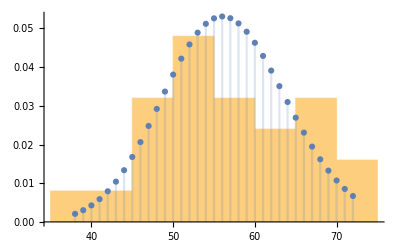

```mathematica
lengths=Length/@lums;
poissonDist=EstimatedDistribution[lengths,PoissonDistribution[λ]]
Show[Histogram[lengths,"Knuth","PDF"],DiscretePlot[PDF[poissonDist,Ni],{Ni,Min[lengths],Max[lengths]}]]
```

```mathematica
replicaDist=SmoothKernelDistribution[lumSum,"Scott","Gaussian"];
{Mean[lumSum],StandardDeviation[lumSum]}
%[[2]]/%[[1]]
NMaximize[{PDF[replicaDist,l],l≥ Min[lumSum]&&l≤ Max[lumSum]},{l},Method->"SimulatedAnnealing"]
Show[Histogram[lumSum,20,"PDF"],Plot[PDF[replicaDist,l],{l,Min[lumSum],Max[lumSum]}] ]
```

SmoothKernelDistribution::rctn: A rectangular array of real numbers is expected at position 1 in SmoothKernelDistribution[lumSum].

{Mean[lumSum],StandardDeviation[lumSum]}

StandardDeviation[lumSum]/Mean[lumSum]

NMaximize::bcons: The following constraints are not valid: {l≥lumSum,l≤lumSum}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMaximize[{PDF[SmoothKernelDistribution[lumSum,Scott,Gaussian],l],l≥lumSum&&l≤lumSum},{l},Method→SimulatedAnnealing]

Histogram::ldata: lumSum is not a valid dataset or list of datasets.

Plot::plln: Limiting value lumSum in {l,Min[lumSum],Max[lumSum]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[lumSum,20,PDF],Plot[PDF[replicaDist,l],{l,Min[lumSum],Max[lumSum]}]].

Show[Histogram[lumSum,20,PDF],Plot[PDF[replicaDist,l],{l,Min[lumSum],Max[lumSum]}]]

```mathematica
binData=Cases[data,binSpec];
Dimensions[binData]
```

{59,2}

## Compare Poisson posterior predictive to distribution of packets across simulations

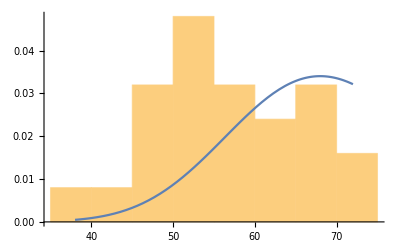

```mathematica
PNgivenn[Ni_,ni_]:=Pochhammer[Ni+ni+1,Ni+ni]/(Pochhammer[ni+1,ni] 2^(3Ni+ni+1/2)Ni!)
Show[Histogram[lengths,"Knuth","PDF"],
Plot[PNgivenn[Ni,lengths[[run-2]]],{Ni,Min[lengths],Max[lengths]}]
]
```

```mathematica
N[Log[Apply[PNgivenn,#]]]&/@{{13, 11},{11,13},{1,2}}
```

{-2.63578,-2.554,-1.50972}

## Estimate distribution P(L|θ) from a single run for one bin First guess yields a ‘hedgehog’ plot with variance of by a factor of 2.

```mathematica
empiricalDist[Ni_,luminosities_]:=Module[{sums},
sums=Take[ListConvolve[Table[1,{i,Ni}],luminosities],{1,-1,Ni}]; (* uncorrelated *)
SmoothKernelDistribution[sums,"Oversmooth","Gaussian"]
]

Needs["MyBinarySearch`"];

PLgivenθ1[Li_,sortedPairs_,νmin_:1.5 10^15,binwidth_:3.925828717905795 10^12]:=Module[{imin,imax,iMultiMin, iMultiMax, ni,li,dist,nMultiBin=3000},

(* index of first element in frequency bin *)
imin=binSearchMin[sortedPairs[[;;,1]], νmin];
imax=binSearchMax[sortedPairs[[;;,1]], νmin+binwidth];
li=Total[sortedPairs[[imin;;imax,2]]];
ni=imax-imin+1;
(*Print[{imin,imax,li}];*)

(* get elements in vicinity *)
(* TODO handle border cases *)
If[ni≥ nMultiBin,
iMultiMin=imin;iMultiMax=imax,

(* half of elements added on either side of bin *)
iMultiMin=imin-Floor[(nMultiBin-ni)/2];
iMultiMax=imax+Floor[(nMultiBin-ni)/2];
];
(*Print[{iMultiMax,iMultiMin}];*)
(*Print[Dimensions[sortedPairs[[iMultiMin;;iMultiMax,2]]]];*)
Sum[
(*NIntegrate[*)
PDF[empiricalDist[Ni,sortedPairs[[iMultiMin;;iMultiMax,2]]],Li] PNgivenn[Ni,ni],{Ni,Max[0,ni-3Floor[√ni]],Min[Length[sortedPairs],ni+3Floor[√ni]]}]

]
(*Plot[PDF[empiricalDist[72,sortedData[[67655;;68654,2]]],Li],{Li,1 10^40,1.1 10^40}]*)
Plot[PLgivenθ1[Li,sortedData,1.1998 10^15,0.0002 10^15],{Li,0.5 10^39,3 10^39}]
```

-Graphics-

```mathematica
Lθ1=Apply[WeightedData,Transpose[Table[{Li,PLgivenθ1[Li,sortedData,1.198 10^15,0.002 10^15]},{Li,1.45 10^40,1.85 10^40,0.025 10^40}]]]
```

WeightedData[…]

Std. dev. only 50% of what it should be

```mathematica
StandardDeviation[Lθ1]
```

1.20329×10^39

## Next approach to estimate P(L|θ). Use central limit theorem because there are many packets in the bin the bootstrap doesn’t do well because there are only 10 samples or so to estimate the pdf by KDE.

```mathematica
PLgivenθ2[Li_,sortedPairs_,νmin_:1.5 10^15,binwidth_:3.925828717905795 10^12]:=Module[{imin,imax,iMultiMin, iMultiMax, ni,li,dist,nMultiBin=3000,mean,var},

(* index of first element in frequency bin *)
imin=binSearchMin[sortedPairs[[;;,1]], νmin];
imax=binSearchMax[sortedPairs[[;;,1]], νmin+binwidth]-1;
li=Total[sortedPairs[[imin;;imax,2]]];
ni=imax-imin+1;
Print[{imin,imax,li}];
Print[{imin,sortedPairs[[imin]]}];
Print[{imax,sortedPairs[[imax]]}];

(* get elements in vicinity *)
(* TODO handle border cases *)
If[ni≥ nMultiBin,
iMultiMin=imin;iMultiMax=imax,

(* half of elements added on either side of bin *)
iMultiMin=imin-Floor[(nMultiBin-ni)/2];
iMultiMax=imax+Floor[(nMultiBin-ni)/2];
];

(* compute mean and variance for CLT *)
mean=Mean[sortedPairs[[iMultiMin;;iMultiMax,2]]];
var=Variance[sortedPairs[[iMultiMin;;iMultiMax,2]]];
(*Print[{Moment[(sortedPairs[[iMultiMin;;iMultiMax,2]]-mean)/stddev,3], Moment[(sortedPairs[[iMultiMin;;iMultiMax,2]]-mean)/stddev,4]}];
*)(*Print[{mean,stddev}];*)
(*Print[{iMultiMax,iMultiMin}];*)
(*Print[Dimensions[sortedPairs[[iMultiMin;;iMultiMax,2]]]];*)
Print[ N[PNgivenn[ni,ni]];PDF[NormalDistribution[ni mean,Sqrt[ni var]],Li]];
(*NIntegrate[*)
Sum[
PDF[NormalDistribution[Ni mean,√(Ni var)],Li] PNgivenn[Ni,ni],

{Ni,Max[0,ni-2Floor[√ni]],Min[Length[sortedPairs],ni+2Floor[√ni]]}
]

]
With[{ν1=1.1998 10^15,binwidth=0.0002 10^15,Lmin=0.5 10^39,Lmax=4 10^39,ΔL=0.5 10^39},
Print[PLgivenθ2[1.66565 10^39,sortedData,ν1,binwidth]];
(*Lθ2=Apply[WeightedData,Transpose[Table[{Li,PLgivenθ2[Li,sortedData,ν1,binwidth]},{Li,Lmin,Lmax,ΔL}]]];
Print[StandardDeviation[Lθ2]];
temp=StringTemplate["`1`, σ=`2`e39"];
dist=SmoothKernelDistribution[Lθ2];
Export["PL.pdf",
Plot[{PDF[SmoothKernelDistribution[Lθ2],Li],PDF[replicaDist,Li]},{Li,Min[lumSum],Max[lumSum]},
PlotLegends->{temp["single run",10^-39 StandardDeviation[dist]],temp[ "250 runs",10^-39 StandardDeviation[replicaDist]]},
PlotLabel->"P(L|θ)",
Frame->True,FrameLabel->"L for ν ∈ [1.198,1.2]x10^15"
]
]*)
]
```

{60022,60033,1.66565×10^39}

{60022,{1.1998×10^15,1.38329×10^38}}

{60033,{1.19998×10^15,1.44311×10^38}}

1.22802×10^-38

9.9483×10^-40

## Why uncertainty underestimated? Poisson seems fine. Either CLT variance too small or I forgot something in my derivation. Didn’t include enough terms in the sum over N_i

## Edgeworth expansion to get asymmetric corrections to Gaussian for CLT. => It can easily get negative depending on γ, the third moment

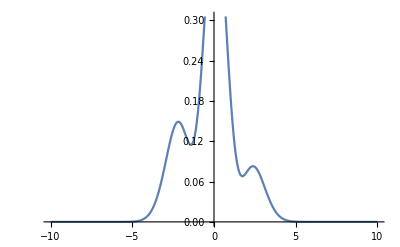

```mathematica
Module[{μ=0,σ=1,γ=-1.12024+0.9,τ=4.8,n=5},

g[x_]:=PDF[NormalDistribution[μ,σ],x](1+(γ HermiteH[3,x])/(6 √n)+((τ-3)HermiteH[4,x])/(24 n)+(γ^2 HermiteH[6,x])/(72n));
Plot[g[x],{x,-10,10}]
]
```

## New try: α-μ distribution

ProbabilityDistribution[((-x+a)^(-1+α μ) ⅇ^(-(-x+a)^α rhat^-α μ) rhat^(-α μ) α μ^μ)/Gamma[μ],{x,-∞,a}]

{0,0,0,0}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{a→1.44496,α→1.07158,μ→1.00014,rhat→0.0317012}

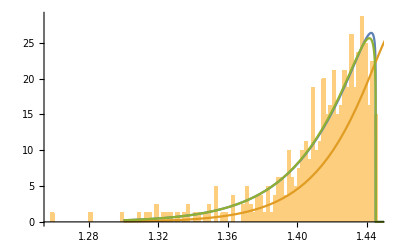

{1.41409,1.41409}

{2.00051,2.00049}

```mathematica
αμ=ProbabilityDistribution[(α μ^μ)/(rhat^(α μ)Gamma[μ])(a-r)^(α μ-1)Exp[-μ (a-r)^α/rhat^α],{r,-∞,a}]
loglikelihood[a_,α_,μ_,rhat_,samples_]:=If[Max[samples]<a,
Length[samples] (Log[α]+μ Log[μ]-α μ Log[rhat]-Log[Gamma[μ]])+(α μ-1)Total[Log[a-samples]]-μ/rhat^α Total[(a-samples)^α],
-10^3]
D[loglikelihood,{{a,α,μ,rhat}}]
testSamples=10^-38 sortedData[[5000;;5400,2]];
(*loglikelihood[1.45 10^38, 1.1,1,0.03 10^39,testSamples]*)
initialGuess={a->1.01 Max[testSamples],α->1.1,μ->1.03,rhat->StandardDeviation[testSamples]};
sol=FindMaximum[loglikelihood[a,α,μ,rhat,testSamples],
{{a,initialGuess[[1,2]]},{α,initialGuess[[2,2]]},{μ,initialGuess[[3,2]]},{rhat,initialGuess[[4,2]]}},MaxIterations->10000][[2]]
Show[Histogram[testSamples,100,"PDF"],Plot[{PDF[αμ,r]/.sol,PDF[αμ,r]/.initialGuess,PDF[αμ,r]/.{a->1.44497,α->1.0383,μ->1.07829,rhat->0.0315}},{r,1.3,1.46},PlotRange->All]]
mom[k_,α_,μ_,rhat_]:=rhat^k Gamma[μ+k/α]/(μ^(k/α)Gamma[μ])
{Mean[testSamples],a-mom[1,α,μ,rhat]/.sol}(* play around to find right right way to include a≠0 *)
{Moment[testSamples,2],mom[2,α,μ,rhat]+a^2-2a mom[1,α,μ,rhat]/.sol}
```

```mathematica
StandardDeviation[testSamples]
```

0.0293004

```mathematica
D[Log[(r-a)/rhat],a]
D[((r-a)/rhat)^α,a]
D[μ Log[μ],μ]
D[Log[Gamma[μ]],μ]
D[((r-a)/rhat)^α,α]
D[Log[(r-a)/rhat],rhat]
D[((r-a)/rhat)^α,rhat]
```

-1/(-a+r)

-(((-a+r)/rhat)^(-1+α) α)/rhat

1+Log[μ]

PolyGamma[0,μ]

((-a+r)/rhat)^α Log[(-a+r)/rhat]

-1/rhat

-((-a+r) ((-a+r)/rhat)^(-1+α) α)/rhat^2

```mathematica
Skewness[testSamples]
```

-1.92382

```mathematica
alphamu[r_,α_,μ_,rhat_,a_]:=α μ^μ/(Gamma[μ]Abs[rhat])((r-a)/rhat)^(α μ-1)Exp[-μ ((r-a)/rhat)^α]
alphamu[1.2, 1.1, 1.4, 0.4, 0.2]
alphamu[1.38, 1.1, 1.4, -0.02, 1.45]
```

0.175734

0.75619

Moments estimator can violate the constraint for a. Damn it!

```mathematica
Table[Moment[testSamples,k],{k,1,4}]
samplemom[0]=1;
samplemom[1]=1.4140908351499886;
samplemom[2]=2.0005092621437472;
samplemom[3]=2.8312755766477258;
samplemom[4]=4.008619184220017;
(*Clear[samplemom];*)
mom[k_]:=∑_(j=0)^k Binomial[k,j](-1)^j a^(k-j) samplemom[j](*/.sol*)
mom[3]
```

{1.41409,2.00051,2.83128,4.00862}

-2.83128+6.00153 a-4.24227 a^2+a^3

0.0308635

{α→1.64234,μ→0.271463,rhat→0.033074,a→1.43798}

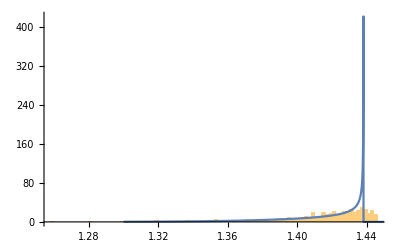

```mathematica
mom[k_,α_,μ_,rhat_]:=rhat^k Gamma[μ+k/α]/(μ^(k/α)Gamma[μ])
mom[1,α,μ,rhat]/.sol

momeqns={Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==mom[1,α,μ,rhat]^2/(mom[2,α,μ,rhat]-mom[1,α,μ,rhat]^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==mom[2,α,μ,rhat]^2/(mom[4,α,μ,rhat]-mom[2,α,μ,rhat]^2),rhat==(μ^(1/α)Gamma[μ]mom[1,α,μ,rhat])/Gamma[μ+1/α]};
momeqns={Gamma[μ+1/α]^2/(Gamma[μ]Gamma[μ+2/α]-Gamma[μ+1/α]^2)==mom[1]^2/(mom[2]-mom[1]^2),Gamma[μ+2/α]^2/(Gamma[μ]Gamma[μ+4/α]-Gamma[μ+2/α]^2)==mom[2]^2/(mom[4]-mom[2]^2),
Gamma[μ+3/α] Gamma[μ]/(Gamma[μ+1/α]Gamma[μ+2/α])==mom[3]/(mom[1]mom[2]),
rhat==(μ^(1/α)Gamma[μ]mom[1])/Gamma[μ+1/α]};
(*momeqns=Table[mom[k,α,μ,rhat]==mom[k],{k,1,4}];*)
FindRoot[momeqns,{{α,1.1},{μ,1.05},{rhat,0.02},{a,1.46}}]
Show[Histogram[testSamples,80,"PDF"],Plot[{PDF[αμ,r]/.%/.sol},{r,1.3,1.46},PlotRange->All]]
```